## Matter Oscillation

### Defining Matter Hamiltonian

```mathematica
fac = Rationalize[4*1.27] ;Vf = {{Ve,0,0},{0,Vu,0},{0,0,Vt}} (*Potential matrix in flavour Basis in eV^2/GeV.*)
```

(Ve | 0 | 0
0 | Vu | 0
0 | 0 | Vt)

```mathematica
Km = 0*E1*IdentityMatrix[3]+1fac/(2E1){{m1^2,0,0},{0,m2^2,0},{0,0,m3^2}} 
(*Removing the Diagonal Energy part from kinetic matrix in mass basis. This does not affect the mixing angles since the eigenvalues of matrix A and A + cI are same and all eigenvalues differing by c.*)
```

((127 m1^2)/(50 E1) | 0 | 0
0 | (127 m2^2)/(50 E1) | 0
0 | 0 | (127 m3^2)/(50 E1))

```mathematica
USMMix={{Cos[ϕ12] Cos[ϕ13],Sin[ϕ12] Cos[ϕ13],Sin[ϕ13]Exp[-I δCP]},{-Sin[ϕ12] Cos[ϕ23]-Cos[ϕ12] Sin[ϕ23] Sin[ϕ13]Exp[I δCP],Cos[ϕ12] Cos[ϕ23]-Sin[ϕ12] Sin[ϕ23] Sin[ϕ13]Exp[I δCP],Sin[ϕ23] Cos[ϕ13]},{Sin[ϕ12] Sin[ϕ23]-Cos[ϕ12] Cos[ϕ23] Sin[ϕ13]Exp[I δCP],-Cos[ϕ12] Sin[ϕ23]-Sin[ϕ12] Cos[ϕ23] Sin[ϕ13]Exp[I δCP],Cos[ϕ23] Cos[ϕ13]}}
```

(cos(ϕ12) cos(ϕ13) | sin(ϕ12) cos(ϕ13) | ⅇ^(-ⅈ δCP) sin(ϕ13)
sin(ϕ12) (-cos(ϕ23))-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23) | cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23) | cos(ϕ13) sin(ϕ23)
sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) cos(ϕ23) | -cos(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) cos(ϕ23) | cos(ϕ13) cos(ϕ23))

```mathematica
Eigenvalues[Km]
```

{(127 m1^2)/(50 E1),(127 m2^2)/(50 E1),(127 m3^2)/(50 E1)}

```mathematica
(*Neutrino mixing angles*)θ12=33.68 Degree;
θ23=41.0 Degree;
θ13=8.52 Degree;
δ=0Degree;
(*Neutrino mixing matrix elements*)
U=SetPrecision[{{Cos[θ12] Cos[θ13],Sin[θ12] Cos[θ13],Sin[θ13]Exp[-I δ]},{-Sin[θ12] Cos[θ23]-Cos[θ12] Sin[θ23] Sin[θ13]Exp[I δ],Cos[θ12] Cos[θ23]-Sin[θ12] Sin[θ23] Sin[θ13]Exp[I δ],Sin[θ23] Cos[θ13]},{Sin[θ12] Sin[θ23]-Cos[θ12] Cos[θ23] Sin[θ13]Exp[I δ],-Cos[θ12] Sin[θ23]-Sin[θ12] Cos[θ23] Sin[θ13]Exp[I δ],Cos[θ23] Cos[θ13]}},30];
```

```mathematica
U
```

(0.8229643391243758321351720042 | 0.548434044365241235574615075166 | 0.148154633780937905473962246106
-0.499410457619914260884996792811 | 0.574128236983643125412868357671 | 0.648818897935257044018442229572
0.270774613561624577506847799668 | -0.607944789005743779775059465464 | 0.746380762192672464472309457051)

```mathematica
Um = {{Ue1,Ue2,Ue3},{Uu1,Uu2,Uu3},{Ut1,Ut2,Ut3}}(*Mixing matrix from mass basis to flavour Basis. Computed by diagonalizing Hamiltonian in flavour basis.*)
```

(Ue1 | Ue2 | Ue3
Uu1 | Uu2 | Uu3
Ut1 | Ut2 | Ut3)

```mathematica
U = Rationalize[U,10^(-20)](*Rationalizing U to increase Precision.*)
```

(6245673449/7589239475 | 4681091308/8535376963 | 1530571178/10330903185
-5823553177/11660855491 | 4662031684/8120192291 | 9456377947/14574757266
2258649739/8341438325 | -7499065501/12335109432 | 9035422075/12105647054)

```mathematica
Kf=U.Km.Transpose[U](*Kinetic matrix in flavour Basis.*)
```

((4954071477606031561327 m1^2)/(2879827790444913781250 E1)+(1391451105448405079864 m2^2)/(1821316497512777584225 E1)+(148758156313693537934 m3^2)/(2668189015446078605625 E1) | -(4619245454966419179071 m1^2)/(4424851240228385361250 E1)+(1385785645593155669672 m2^2)/(1732722555393289805825 E1)+(919077380406016234441 m3^2)/(3764260156498032305250 E1) | (1791562165593811135997 m1^2)/(3165258650718393968750 E1)-(1114545978131607048529 m2^2)/(1316060111024710187700 E1)+(35126565787012284049 m3^2)/(125062267706654466990 E1)
-(4619245454966419179071 m1^2)/(4424851240228385361250 E1)+(1385785645593155669672 m2^2)/(1732722555393289805825 E1)+(919077380406016234441 m3^2)/(3764260156498032305250 E1) | (4307048993879042752783 m1^2)/(6798777539099242554050 E1)+(1380143253336362116856 m2^2)/(1648438071070395717025 E1)+(11356731652316507720743 m3^2)/(10621177468140989737800 E1) | -(1670477591637026191981 m1^2)/(4863415344745704628750 E1)-(1110007970672193344467 m2^2)/(1252043256479597358900 E1)+(434047219543484258527 m3^2)/(352873734719835988728 E1)
(1791562165593811135997 m1^2)/(3165258650718393968750 E1)-(1114545978131607048529 m2^2)/(1316060111024710187700 E1)+(35126565787012284049 m3^2)/(125062267706654466990 E1) | -(1670477591637026191981 m1^2)/(4863415344745704628750 E1)-(1110007970672193344467 m2^2)/(1252043256479597358900 E1)+(434047219543484258527 m3^2)/(352873734719835988728 E1) | (647890327722565551367 m1^2)/(3478979666488940281250 E1)+(7141969890312624387127 m2^2)/(7607746234970768131200 E1)+(414725368532858312575 m3^2)/(293093381192037757832 E1))

```mathematica
Hf = Kf+Vf(*Total Hamiltonian matrix in flavour Basis.*)
```

((4954071477606031561327 m1^2)/(2879827790444913781250 E1)+(1391451105448405079864 m2^2)/(1821316497512777584225 E1)+(148758156313693537934 m3^2)/(2668189015446078605625 E1)+Ve | -(4619245454966419179071 m1^2)/(4424851240228385361250 E1)+(1385785645593155669672 m2^2)/(1732722555393289805825 E1)+(919077380406016234441 m3^2)/(3764260156498032305250 E1) | (1791562165593811135997 m1^2)/(3165258650718393968750 E1)-(1114545978131607048529 m2^2)/(1316060111024710187700 E1)+(35126565787012284049 m3^2)/(125062267706654466990 E1)
-(4619245454966419179071 m1^2)/(4424851240228385361250 E1)+(1385785645593155669672 m2^2)/(1732722555393289805825 E1)+(919077380406016234441 m3^2)/(3764260156498032305250 E1) | (4307048993879042752783 m1^2)/(6798777539099242554050 E1)+(1380143253336362116856 m2^2)/(1648438071070395717025 E1)+(11356731652316507720743 m3^2)/(10621177468140989737800 E1)+Vu | -(1670477591637026191981 m1^2)/(4863415344745704628750 E1)-(1110007970672193344467 m2^2)/(1252043256479597358900 E1)+(434047219543484258527 m3^2)/(352873734719835988728 E1)
(1791562165593811135997 m1^2)/(3165258650718393968750 E1)-(1114545978131607048529 m2^2)/(1316060111024710187700 E1)+(35126565787012284049 m3^2)/(125062267706654466990 E1) | -(1670477591637026191981 m1^2)/(4863415344745704628750 E1)-(1110007970672193344467 m2^2)/(1252043256479597358900 E1)+(434047219543484258527 m3^2)/(352873734719835988728 E1) | (647890327722565551367 m1^2)/(3478979666488940281250 E1)+(7141969890312624387127 m2^2)/(7607746234970768131200 E1)+(414725368532858312575 m3^2)/(293093381192037757832 E1)+Vt)

```mathematica
Kf /.{m1->0,m2^2->7.59*10^(-5),m3^2->2.32*10^(-3),E1->1}
 (*Hamiltonian matrix with experimental values for mass states and potential in some medium.*)
```

(0.000187332 | 0.000627151 | 0.000587346
0.000627151 | 0.00254421 | 0.00278639
0.000587346 | 0.00278639 | 0.00335404)

```mathematica
Km/.{m1->0m2^2->7.59*10^(-5),m3^2->2.32*10^(-3)} //Eigenvalues (*Cross checking eigenvalues for kinetic matrix.*)
```

{0.0058928/E1,(2.54 m2^2)/E1,(2.54 (0→0.0000759)^2)/E1}

```mathematica
energy = Power[10,6] (*Energy in GeV, L in Km and m in eV.*)
```

1000000

```mathematica
Ptau =100 Power[10,-11];Pmue = 00Power[10,-11];Pe = Power[10,-4]*0; (*In eV^2/GeV.*)
```

```mathematica
evc=Eigenvectors[N[Hf/.{Vt->Ptau,Vu->Pmue,m1->0,Ve->Pe,m2^2->Rationalize[7.59*10^(-5)],m3^2->Rationalize[2.32*10^(-3)],E1->energy},30]](*Eigenvectors of Hamiltonian matrix in flavour Basis (Not normalized).*)
```

(-0.132751198719181886345372790581 | -0.585551155033860119913259594047 | -0.799691793178554879090748397961
-0.304423033453249790093968146456 | -0.743745489857517760880031886858 | 0.595121217080791452991377393898
-0.943241080499435118129806310598 | 0.322447656457778051924886616262 | -0.079522153536891237090421164349)

```mathematica
en1 = Normalize[evc[[1]]];
en2 = Normalize[evc[[2]]];
en3 = Normalize[evc[[3]]]; (*Normalizing Eigenvectors.*)
```

```mathematica
env = {en3,en2,en1} (*Flavour Mixing Matrix.*)
```

(-0.943241080499435118129806310598 | 0.322447656457778051924886616262 | -0.079522153536891237090421164349
-0.304423033453249790093968146456 | -0.743745489857517760880031886858 | 0.595121217080791452991377393898
-0.132751198719181886345372790581 | -0.585551155033860119913259594047 | -0.799691793178554879090748397961)

```mathematica
U//N
```

(0.822964 | 0.548434 | 0.148155
-0.49941 | 0.574128 | 0.648819
0.270775 | -0.607945 | 0.746381)

```mathematica
UM=Inverse[SetPrecision[env,25]] (*Flavour mixing matrix from mass basis to flavour basis.*)
```

(-0.9432410804994351181298063 | -0.3044230334532497900939681 | -0.1327511987191818863453728
0.3224476564577780519248866 | -0.7437454898575177608800319 | -0.5855511550338601199132596
-0.07952215353689123709042116 | 0.5951212170807914529913774 | -0.7996917931785548790907484)

```mathematica
eval=N[Eigenvalues[Hf/.{Vt->Ptau,Vu->Pmue,m1->0,Ve->Pe,m2^2->Rationalize[7.59*10^(-5)],m3^2->Rationalize[2.32*10^(-3)]}],30]//Reverse 
(*Eigenvalues of Hamiltonian in increasing order.*)
```

{0,0.000192785999999999999355906577283/E1,0.00589280000000000006026344928614/E1}

```mathematica
ep[x_]:=SetPrecision[Evaluate[eval] /. E1->x,25] (*To get precision evaluation of function.*)
```

## Coherent Limit - Flavour Oscillation

## Probability From electron neutrino

#### P e --> e

```mathematica
Clear[flavorα,flavorβ];flavorα=1;flavorβ=1;mf=1;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Petoe = P/.{flavorα->1,flavorβ->1}//N
```

2. (0.204527 cos((0.000192786 L)/E1)+0.00746497 cos((0.00570001 L)/E1)+0.0164079 cos((0.0058928 L)/E1))+0.5432

```mathematica
Pee[L_,E1_]:=Evaluate[Petoe]
```

```mathematica
Pee[y1,y2]
```

2. (0.204527 cos((0.000192786 y1)/y2)+0.00746497 cos((0.00570001 y1)/y2)+0.0164079 cos((0.0058928 y1)/y2))+0.5432

```mathematica
Pee[l,1]
```

2. (0.204527 cos(0.000192786 l)+0.00746497 cos(0.00570001 l)+0.0164079 cos(0.0058928 l))+0.5432

```mathematica
result=Maximize[{Pee[xt,yt],xt>0,yt>0},{xt,yt}]
```

{1.,{xt→8.49918×10^-7,yt→0.196095}}

#### P e --> μ

```mathematica
Clear[flavorα,flavorβ];flavorα=1;flavorβ=2;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
UM
```

(0.8188307443279101730180041 | -0.5523083109015990429978499 | 0.1564344650402308683430276
-0.5117297730355971403385411 | -0.5788504664074381005590548 | 0.6348738275664130832665387
0.2600939282881029499531816 | 0.5999063820704977187549709 | 0.7566131648463098036695469)

```mathematica
Umat
```

(0.175577819858516088755984 | -0.133962360651691587315676 | -0.0416154592068245014403078
-0.133962360651691587315676 | 0.102210598615673903146467 | 0.0317517620360176841692094
-0.0416154592068245014403078 | 0.0317517620360176841692094 | 0.00986369717080681727109834)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
Imag/.{E1->3}
```

0

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Petomu = P/.{flavorα->1,flavorβ->2};
```

```mathematica
Pemu[L_,E1_]:=Evaluate[Petomu]
```

```mathematica
Pemu[y1,y2]//N
```

2. (-0.133962 cos((0.000192786 y1)/y2)+0.0317518 cos((0.00570001 y1)/y2)-0.0416155 cos((0.0058928 y1)/y2))+0.287652

```mathematica
Pemu[1,2];
```

#### P e --> τ

```mathematica
Clear[flavorα,flavorβ];flavorα=1;flavorβ=3;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.0453574582195499228902908 | -0.0705650112537128335217682 | 0.0252075530341629106314774
-0.0705650112537128335217682 | 0.109781742820200498670868 | -0.0392167315664876651490994
0.0252075530341629106314774 | -0.0392167315664876651490994 | 0.014009178532324754517622)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
Imag /.{E1->3}
```

0

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Petotau = P/.{flavorα->1,flavorβ->3};
```

```mathematica
Petau[L_,E1_]:=Evaluate[Petotau]
```

```mathematica
Petau[y1,y2];
```

```mathematica
Petau[L,2];
```

```mathematica
Pemu[x,1]
```

2 (-0.133962360651691587315676 cos(0.000192786000000000001393976577473304102052996341490292035848223 x)+0.0317517620360176841692094 cos(0.0057000140000000000205257103001845373116893992219512751158756 x)-0.0416154592068245014403078 cos(0.00589280000000000002191968687765784141374239556344156715172385 x))+0.287652115644996809173549

```mathematica
result=Maximize[{Pemu[1,yt],yt>0},yt]
```

{0.702001673187610021581411,{yt→0.0000604974330500980679959917}}

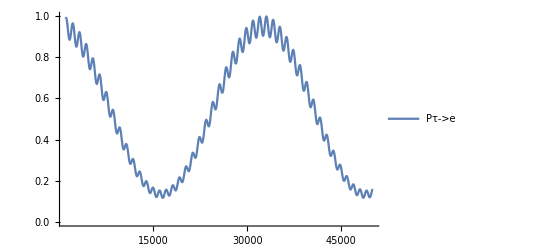

```mathematica
Plot[Evaluate[{Pee[x,1]}],{x,Power[10,4]*0.1,Power[10,4]*5},PlotPoints->10000,(*Adjust based on desired level of detail*)MaxRecursion->3,(*Adjust based on desired level of detail*)PlotLegends->{"Pτ->e","Pτ->μ","Pτ->τ","Total Probability"}]
```

```mathematica
y=energy;losc= energy;
```

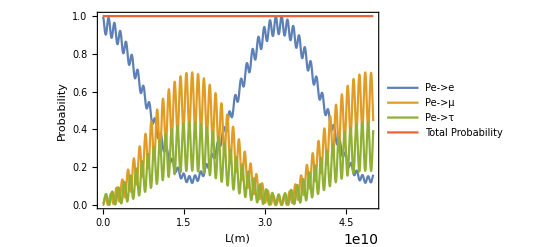

```mathematica
pe=Plot[Evaluate[{Pee[x,y],Pemu[x,y],Petau[x,y],Pee[x,y]+Pemu[x,y]+Petau[x,y]}],{x,Power[10,-5],Power[10,4]*energy*5},PlotPoints->10000,(*Adjust based on desired level of detail*)MaxRecursion->3,(*Adjust based on desired level of detail*)Frame->True,FrameLabel->{"L(m)",Rotate[Style["Probability"],0 Degree]},PlotLegends->{"Pe->e","Pe->μ","Pe->τ","Total Probability"}]
```

```mathematica
(*Export["PeesunTev.png",pe,ImageResolution->300]*)
```

```mathematica
Petau[x,1]
```

2 (-0.0705650112537128335217682 cos(0.000192786000000000001393976577473304102052996341490292035848223 x)-0.0392167315664876651490994 cos(0.0057000140000000000205257103001845373116893992219512751158756 x)+0.0252075530341629106314774 cos(0.00589280000000000002191968687765784141374239556344156715172385 x))+0.16914837957207517607878

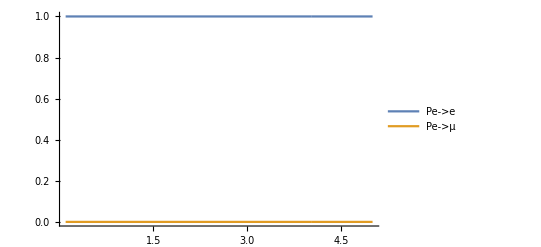

```mathematica
Plot[Evaluate[{Pee[Power[10,-7]*x,1],Pemu[Power[10,-7]*x,1]}],{x,.1,5},PlotPoints->10000,(*Adjust based on desired level of detail*)MaxRecursion->3,(*Adjust based on desired level of detail*)PlotLegends->{"Pe->e","Pe->μ","Pe->τ","Total Probability"}]
```

## Probability From μ neutrino

#### P μ --> e

```mathematica
Clear[flavorα,flavorβ];flavorα=2;flavorβ=1;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.175577819858516088755984 | -0.133962360651691587315676 | -0.0416154592068245014403078
-0.133962360651691587315676 | 0.102210598615673903146467 | 0.0317517620360176841692094
-0.0416154592068245014403078 | 0.0317517620360176841692094 | 0.00986369717080681727109834)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
Imag /.{E1->2}
```

0

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Pμtoe = P/.{flavorα->2,flavorβ->1};
```

```mathematica
Pμtoe /.{x->2}
```

2 (-0.133962360651691587315676 cos((0.000192786000000000001393976577473304102052996341490292035848223 L)/E1)+0.0317517620360176841692094 cos((0.0057000140000000000205257103001845373116893992219512751158756 L)/E1)-0.0416154592068245014403078 cos((0.00589280000000000002191968687765784141374239556344156715172385 L)/E1))+0.287652115644996809173549

```mathematica
Pμe[L_,E1_]:=Evaluate[Pμtoe]
```

```mathematica
Pμe[y1,y2];
```

```mathematica
Pμe[1000,2]
```

0.041798554265993186118701

#### P μ --> μ

```mathematica
Clear[flavorα,flavorβ];flavorα=2;flavorβ=2;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.068574514553404908714301 | 0.087743336768019579510541 | 0.105549509289639273866207
0.087743336768019579510541 | 0.112270472453586270688115 | 0.135054053238502774716877
0.105549509289639273866207 | 0.135054053238502774716877 | 0.162461214400685564410334)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
Imag/.{E1->3}
```

0

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Pμtomu = P/.{flavorα->2,flavorβ->2};
```

```mathematica
Pμmu[L_,E1_]:=Evaluate[Pμtomu]
```

```mathematica
Pμmu[y1,y2];
```

```mathematica
Pμmu[L,2]
```

2 (0.087743336768019579510541 cos(0.0000963930000000000006969882887366520510264981707451460179241114 L)+0.135054053238502774716877 cos(0.0028500070000000000102628551500922686558446996109756375579378 L)+0.105549509289639273866207 cos(0.00294640000000000001095984343882892070687119778172078357586192 L))+0.34330620140767674381275

#### P μ --> τ

```mathematica
Clear[flavorα,flavorβ];flavorα=2;flavorβ=3;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.0177150261991427646207638 | 0.0462190238836720078051352 | -0.063934050082814772425899
0.0462190238836720078051352 | 0.120586791390848451080951 | -0.166805815274520458886086
-0.063934050082814772425899 | -0.166805815274520458886086 | 0.230739865357335231311985)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
Imag /.{E1->3}
```

0

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Pμtotau = P/.{flavorα->2,flavorβ->3};
```

```mathematica
Pμtau[L_,E1_]:=Evaluate[Pμtotau]
```

```mathematica
Pμtau[y1,y2];
```

```mathematica
Pμtau[L,2]
```

2 (0.0462190238836720078051352 cos(0.0000963930000000000006969882887366520510264981707451460179241114 L)-0.166805815274520458886086 cos(0.0028500070000000000102628551500922686558446996109756375579378 L)-0.063934050082814772425899 cos(0.00294640000000000001095984343882892070687119778172078357586192 L))+0.369041682947326447013701

```mathematica
Pμe[L,0.00000002]
```

2 (-0.133962360651691587315676 cos(9639.3 L)+0.0317517620360176841692094 cos(285001. L)-0.0416154592068245014403078 cos(294640. L))+0.287652115644996809173549

```mathematica
y=energy;
```

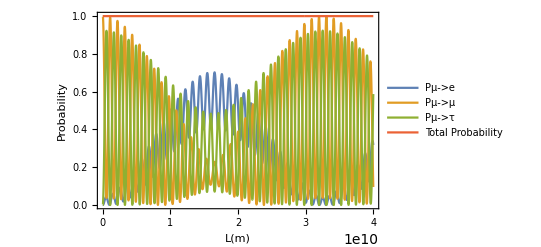

```mathematica
pmu=Plot[Evaluate[{Pμe[x,y],Pμmu[x,y],Pμtau[x,y],Pμe[x,y]+Pμmu[x,y]+Pμtau[x,y]}],{x,Power[10,-4],Power[10,4]*energy*4.0},PlotPoints->10000,(*Adjust based on desired level of detail*)MaxRecursion->3,(*Adjust based on desired level of detail*)Frame->True,FrameLabel->{"L(m)",Rotate[Style["Probability"],0 Degree]},PlotLegends->{"Pμ->e","Pμ->μ","Pμ->τ","Total Probability"}]
```

```mathematica
(*Export["PmusunTev.png",pmu,ImageResolution->300]*)
```

## Probability From τ neutrino

#### P τ --> e

```mathematica
Clear[flavorα,flavorβ];flavorα=3;flavorβ=1;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.0453574582195499228902908 | -0.0705650112537128335217682 | 0.0252075530341629106314774
-0.0705650112537128335217682 | 0.109781742820200498670868 | -0.0392167315664876651490994
0.0252075530341629106314774 | -0.0392167315664876651490994 | 0.014009178532324754517622)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
Imag /.{E1->2}
```

0

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Pτtoe = P/.{flavorα->3,flavorβ->1};
```

```mathematica
Pτtoe /.{x->2}
```

2 (-0.0705650112537128335217682 cos((0.000192786000000000001393976577473304102052996341490292035848223 L)/E1)-0.0392167315664876651490994 cos((0.0057000140000000000205257103001845373116893992219512751158756 L)/E1)+0.0252075530341629106314774 cos((0.00589280000000000002191968687765784141374239556344156715172385 L)/E1))+0.16914837957207517607878

```mathematica
Pτe[L_,E1_]:=Evaluate[Pτtoe]
```

```mathematica
Pτe[y1,y2];
```

```mathematica
Pτe[1000,2]
```

0.054338500543109684471663

#### P τ --> μ

```mathematica
Clear[flavorα,flavorβ];flavorα=3;flavorβ=2;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.0177150261991427646207638 | 0.0462190238836720078051352 | -0.063934050082814772425899
0.0462190238836720078051352 | 0.120586791390848451080951 | -0.166805815274520458886086
-0.063934050082814772425899 | -0.166805815274520458886086 | 0.230739865357335231311985)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
Imag/.{E1->3}
```

0

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Pτtomu = P/.{flavorα->3,flavorβ->2};
```

```mathematica
Pτmu[L_,E1_]:=Evaluate[Pτtomu]
```

```mathematica
Pτmu[y1,y2];
```

```mathematica
Pτmu[L,2]
```

2 (0.0462190238836720078051352 cos(0.0000963930000000000006969882887366520510264981707451460179241114 L)-0.166805815274520458886086 cos(0.0028500070000000000102628551500922686558446996109756375579378 L)-0.063934050082814772425899 cos(0.00294640000000000001095984343882892070687119778172078357586192 L))+0.369041682947326447013701

#### P τ --> τ

```mathematica
Clear[flavorα,flavorβ];flavorα=3;flavorβ=3;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.00457636711364415241536955 | 0.024345987370040825716633 | 0.0387264970486518617944216
0.024345987370040825716633 | 0.129519133037865037048247 | 0.206022546841008124035186
0.0387264970486518617944216 | 0.206022546841008124035186 | 0.327714437329089187443902)

```mathematica
n=Length[Umat];
Rea=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Rea+=Re[Umat[[i,j]]]*Cos[mf*(eval[[j]]-eval[[i]])*L];];];
Rea;
```

```mathematica
n=Length[Umat];
Imag=0;
For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,Imag+=Im[Umat[[i,j]]]*Sin[mf*(eval[[j]]-eval[[i]])*L];];];
Imag;
```

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]+2*Rea-2*0*Imag  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
Pτtotau = P/.{flavorα->3,flavorβ->3};
```

```mathematica
Pτtau[L_,E1_]:=Evaluate[Pτtotau]
```

```mathematica
Pτtau[y1,y2];
```

```mathematica
Pτtau[L,2]
```

2 (0.024345987370040825716633 cos(0.0000963930000000000006969882887366520510264981707451460179241114 L)+0.206022546841008124035186 cos(0.0028500070000000000102628551500922686558446996109756375579378 L)+0.0387264970486518617944216 cos(0.00294640000000000001095984343882892070687119778172078357586192 L))+0.461809937480598376907519

```mathematica
Pτe[L,0.00000002]
```

2 (-0.0705650112537128335217682 cos(9639.3 L)-0.0392167315664876651490994 cos(285001. L)+0.0252075530341629106314774 cos(294640. L))+0.16914837957207517607878

```mathematica
y=energy;
```

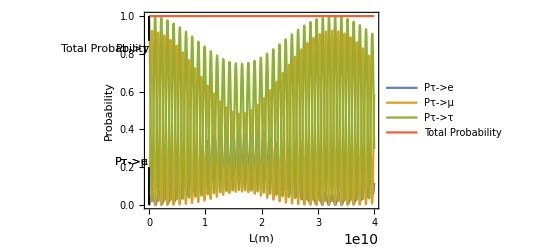

```mathematica
ptau=Plot[Evaluate[{Pτe[x,y],Pτmu[x,y],Pτtau[x,y],Pτe[x,y]+Pτmu[x,y]+Pτtau[x,y]}],{x,Power[10,-3],Power[10,4]*energy*4},(*Adjust based on desired level of detail*)Frame->True,FrameLabel->{{"Probability",None},{"L(m)",None}},PlotLegends->{"Pτ->e","Pτ->μ","Pτ->τ","Total Probability"},LabelStyle->{FontFamily->"Arial",FontSize->12},ImagePadding->40,PlotRangePadding->{{Automatic,Automatic},{Automatic,Automatic}},PlotStyle->Automatic,Epilog->{Text["Pτ->τ",{0.001,0.8},{1,-1}],Text["Total Probability",{0.003,0.8},{1,-1}],Text["Pτ->e",{0.002,0.2},{1,-1}],Text["Pτ->μ",{0.0035,0.2},{1,-1}],Line[{{0.001,0.87},{0.0013,1}}],Line[{{0.003,0.87},{0.0035,1}}],,Line[{{0.002,0.2},{0.0014,0}}],Line[{{0.0035,0.2},{0.0039,0}}]}]
```

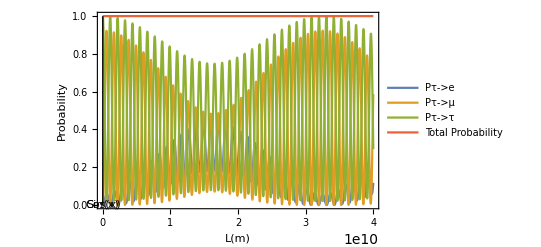

```mathematica
ptau=Plot[Evaluate[{Pτe[x,y],Pτmu[x,y],Pτtau[x,y],Pτe[x,y]+Pτmu[x,y]+Pτtau[x,y]}],{x,Power[10,-4],Power[10,4]*energy*4},PlotPoints->10000,(*Adjust based on desired level of detail*)MaxRecursion->3,(*Adjust based on desired level of detail*)Frame->True,FrameLabel->{"L(m)",Rotate[Style["Probability"],0 Degree]},PlotLegends->{"Pτ->e","Pτ->μ","Pτ->τ","Total Probability"},Epilog->{Text["Sin(x)",{0.1,0.001}],Text["Cos(x)",{3 Pi/2,Cos[3 Pi/2]}],Line[{{Pi,Sin[Pi/2]},{Pi,Sin[Pi]}}],Line[{{3 Pi/2,Cos[3 Pi/2]},{3 Pi/2-0.5,Cos[3 Pi/2]}}]}]
```

```mathematica
(*Export["PtausunTev.png",ptau,ImageResolution->300]*)
```

## Decoherence Limit - No Oscillation only mixing

## Probability From electron neutrino

#### P e --> e

```mathematica
Clear[flavorα,flavorβ];flavorα=1;flavorβ=1;mf=1;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
n=Length[Umat];
```

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}] /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPetoe = P/.{flavorα->1,flavorβ->1}//N
```

0.549645

#### P e --> μ

```mathematica
Clear[flavorα,flavorβ];flavorα=1;flavorβ=2;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
UM
```

(-0.8229643391243758891388285 | -0.548434044365241251937013 | -0.1481546337809379028499268
0.4994104576199142316856465 | -0.5741282369836431940386969 | -0.6488188979352570387495172
-0.2707746135616245087304457 | 0.6079447890057437029322482 | -0.7463807621926724627364997)

```mathematica
Umat
```

(0.168918531713150091523766 | -0.12941122908435860457704 | -0.0395073026287914869467263
-0.12941122908435860457704 | 0.0991440432454374048675331 | 0.0302671858389211997095066
-0.0395073026287914869467263 | 0.0302671858389211997095066 | 0.00924011678987028723721969)

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPetomu = P/.{flavorα->1,flavorβ->2};
```

#### P e --> τ

```mathematica
Clear[flavorα,flavorβ];flavorα=1;flavorβ=3;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.0496567077943548365820141 | -0.0742980657564576274953784 | 0.0246413579621027909133643
-0.0742980657564576274953784 | 0.111167308916489609739981 | -0.0368692431600319822446025
0.0246413579621027909133643 | -0.0368692431600319822446025 | 0.0122278851979291913312382)

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}] /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPetotau = P/.{flavorα->1,flavorβ->3};
```

## Probability From μ neutrino

#### P μ --> e

```mathematica
Clear[flavorα,flavorβ];flavorα=2;flavorβ=1;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.168918531713150091523766 | -0.12941122908435860457704 | -0.0395073026287914869467263
-0.12941122908435860457704 | 0.0991440432454374048675331 | 0.0302671858389211997095066
-0.0395073026287914869467263 | 0.0302671858389211997095066 | 0.00924011678987028723721969)

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}] /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPμtoe = P/.{flavorα->2,flavorβ->1};
```

#### P μ --> μ

```mathematica
Clear[flavorα,flavorβ];flavorα=2;flavorβ=2;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
Umat
```

(0.0622057497406018335486105 | 0.0822115958243883470700806 | 0.104993459615141968259468
0.0822115958243883470700806 | 0.108651475405032187635541 | 0.138760161272525825955618
0.104993459615141968259468 | 0.138760161272525825955618 | 0.177212341430253696245516)

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]/.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPμtomu = P/.{flavorα->2,flavorβ->2};
```

#### P μ --> τ

```mathematica
Clear[flavorα,flavorβ];flavorα=2;flavorβ=3;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]  /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPμtotau = P/.{flavorα->2,flavorβ->3};
```

## Probability From τ neutrino

#### P τ --> e

```mathematica
Clear[flavorα,flavorβ];flavorα=3;flavorβ=1;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}]/.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPτtoe = P/.{flavorα->3,flavorβ->1};
```

#### P τ --> μ

```mathematica
Clear[flavorα,flavorβ];flavorα=3;flavorβ=2;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}] /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPτtomu = P/.{flavorα->3,flavorβ->2};
```

#### P τ --> τ

```mathematica
Clear[flavorα,flavorβ];flavorα=3;flavorβ=3;
```

```mathematica
v1 = Table[UM[[flavorα,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}];
v2 = Table[UM[[flavorβ,i]]*Conjugate[UM[[flavorα,i]]],{i,1,3}];
```

```mathematica
Umat = Outer[Times,v1,v2];
```

```mathematica
P =Sum[UM[[flavorα,i]]*Conjugate[UM[[flavorα,i]]]*UM[[flavorβ,i]]*Conjugate[UM[[flavorβ,i]]],{i,1,3}] /.{m2^2->7.59*10^(-5),m1->0,m3^2->2.32*10^(-3)};(*Probability Formula.*)
```

```mathematica
DPτtotau = P/.{flavorα->3,flavorβ->3};
```

```mathematica
Probmat= {{DPetoe,DPetomu,DPetotau},{DPμtoe,DPμtomu,DPμtotau},{DPτtoe,DPτtomu,DPτtotau}}
```

(0.549645 | 0.277302691748457783628519 | 0.173051901908773637653233
0.277302691748457783628519 | 0.348069566575887717429668 | 0.374627741675654498941814
0.173051901908773637653233 | 0.374627741675654498941814 | 0.452320356415571863404953)

```mathematica
Sum[Probmat[[i,1]],{i,1,3}]
Sum[Probmat[[2,i]],{i,1,3}]
Sum[Probmat[[3,i]],{i,1,3}]
```

1.

1.

1.

## Neutrino Triangle

### SM Mixing Probability

```mathematica
SMMixProbmat= {{DSMPetoe,DSMPetomu,DSMPetotau},{DSMPμtoe,DSMPμtomu,DSMPμtotau},{DSMPτtoe,DSMPτtomu,DSMPτtotau}};
```

```mathematica
DSMPetoe =Sum[USMMix[[1,i]]*Conjugate[USMMix[[1,i]]]*USMMix[[1,i]]*Conjugate[USMMix[[1,i]]],{i,1,3}];
DSMPetomu =Sum[USMMix[[2,i]]*Conjugate[USMMix[[2,i]]]*USMMix[[1,i]]*Conjugate[USMMix[[1,i]]],{i,1,3}];
DSMPetotau =Sum[USMMix[[3,i]]*Conjugate[USMMix[[3,i]]]*USMMix[[1,i]]*Conjugate[USMMix[[1,i]]],{i,1,3}];
DSMPμtoe =Sum[USMMix[[1,i]]*Conjugate[USMMix[[1,i]]]*USMMix[[2,i]]*Conjugate[USMMix[[2,i]]],{i,1,3}];
DSMPμtomu =Sum[USMMix[[2,i]]*Conjugate[USMMix[[2,i]]]*USMMix[[2,i]]*Conjugate[USMMix[[2,i]]],{i,1,3}];
DSMPμtotau =Sum[USMMix[[3,i]]*Conjugate[USMMix[[3,i]]]*USMMix[[2,i]]*Conjugate[USMMix[[2,i]]],{i,1,3}];
DSMPτtoe =Sum[USMMix[[1,i]]*Conjugate[USMMix[[1,i]]]*USMMix[[3,i]]*Conjugate[USMMix[[3,i]]],{i,1,3}];
DSMPτtomu =Sum[USMMix[[2,i]]*Conjugate[USMMix[[2,i]]]*USMMix[[3,i]]*Conjugate[USMMix[[3,i]]],{i,1,3}];
DSMPτtotau =Sum[USMMix[[3,i]]*Conjugate[USMMix[[3,i]]]*USMMix[[3,i]]*Conjugate[USMMix[[3,i]]],{i,1,3}];
(*Probability Formula.*)
```

```mathematica
SMMixProbmat
```

(ⅇ^(2 ⅈ Conjugate[δCP]-2 ⅈ δCP) sin^2(ϕ13) (Conjugate[sin(ϕ13)])^2+cos^2(ϕ12) cos^2(ϕ13) (Conjugate[(cos(ϕ12) cos(ϕ13))])^2+sin^2(ϕ12) cos^2(ϕ13) (Conjugate[(cos(ϕ13) sin(ϕ12))])^2 | cos(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ12) cos(ϕ13))] (sin(ϕ12) (-cos(ϕ23))-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(-cos(ϕ23) sin(ϕ12)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23))]+sin(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ13) sin(ϕ12))] (cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23))]+ⅇ^(ⅈ Conjugate[δCP]-ⅈ δCP) sin(ϕ13) cos(ϕ13) sin(ϕ23) Conjugate[sin(ϕ13)] Conjugate[(cos(ϕ13) sin(ϕ23))] | sin(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ13) sin(ϕ12))] (-cos(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) cos(ϕ23)) Conjugate[(-ⅇ^(ⅈ δCP) cos(ϕ23) sin(ϕ12) sin(ϕ13)-cos(ϕ12) sin(ϕ23))]+cos(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ12) cos(ϕ13))] (sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) cos(ϕ23)) Conjugate[(sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) cos(ϕ23) sin(ϕ13))]+ⅇ^(ⅈ Conjugate[δCP]-ⅈ δCP) sin(ϕ13) cos(ϕ13) cos(ϕ23) Conjugate[sin(ϕ13)] Conjugate[(cos(ϕ13) cos(ϕ23))]
cos(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ12) cos(ϕ13))] (sin(ϕ12) (-cos(ϕ23))-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(-cos(ϕ23) sin(ϕ12)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23))]+sin(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ13) sin(ϕ12))] (cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23))]+ⅇ^(ⅈ Conjugate[δCP]-ⅈ δCP) sin(ϕ13) cos(ϕ13) sin(ϕ23) Conjugate[sin(ϕ13)] Conjugate[(cos(ϕ13) sin(ϕ23))] | (sin(ϕ12) (-cos(ϕ23))-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23))^2 (Conjugate[(-cos(ϕ23) sin(ϕ12)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23))])^2+(cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23))^2 (Conjugate[(cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23))])^2+cos^2(ϕ13) sin^2(ϕ23) (Conjugate[(cos(ϕ13) sin(ϕ23))])^2 | (sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) cos(ϕ23)) (sin(ϕ12) (-cos(ϕ23))-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) cos(ϕ23) sin(ϕ13))] Conjugate[(-cos(ϕ23) sin(ϕ12)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23))]+(-cos(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) cos(ϕ23)) (cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(-ⅇ^(ⅈ δCP) cos(ϕ23) sin(ϕ12) sin(ϕ13)-cos(ϕ12) sin(ϕ23))] Conjugate[(cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23))]+cos^2(ϕ13) sin(ϕ23) cos(ϕ23) Conjugate[(cos(ϕ13) cos(ϕ23))] Conjugate[(cos(ϕ13) sin(ϕ23))]
sin(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ13) sin(ϕ12))] (-cos(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) cos(ϕ23)) Conjugate[(-ⅇ^(ⅈ δCP) cos(ϕ23) sin(ϕ12) sin(ϕ13)-cos(ϕ12) sin(ϕ23))]+cos(ϕ12) cos(ϕ13) Conjugate[(cos(ϕ12) cos(ϕ13))] (sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) cos(ϕ23)) Conjugate[(sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) cos(ϕ23) sin(ϕ13))]+ⅇ^(ⅈ Conjugate[δCP]-ⅈ δCP) sin(ϕ13) cos(ϕ13) cos(ϕ23) Conjugate[sin(ϕ13)] Conjugate[(cos(ϕ13) cos(ϕ23))] | (sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) cos(ϕ23)) (sin(ϕ12) (-cos(ϕ23))-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) cos(ϕ23) sin(ϕ13))] Conjugate[(-cos(ϕ23) sin(ϕ12)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) sin(ϕ23))]+(-cos(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) cos(ϕ23)) (cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23)) Conjugate[(-ⅇ^(ⅈ δCP) cos(ϕ23) sin(ϕ12) sin(ϕ13)-cos(ϕ12) sin(ϕ23))] Conjugate[(cos(ϕ12) cos(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) sin(ϕ23))]+cos^2(ϕ13) sin(ϕ23) cos(ϕ23) Conjugate[(cos(ϕ13) cos(ϕ23))] Conjugate[(cos(ϕ13) sin(ϕ23))] | (-cos(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) sin(ϕ12) sin(ϕ13) cos(ϕ23))^2 (Conjugate[(-ⅇ^(ⅈ δCP) cos(ϕ23) sin(ϕ12) sin(ϕ13)-cos(ϕ12) sin(ϕ23))])^2+(sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) sin(ϕ13) cos(ϕ23))^2 (Conjugate[(sin(ϕ12) sin(ϕ23)-ⅇ^(ⅈ δCP) cos(ϕ12) cos(ϕ23) sin(ϕ13))])^2+cos^2(ϕ13) cos^2(ϕ23) (Conjugate[(cos(ϕ13) cos(ϕ23))])^2)

### Generating SM Mixing random points

```mathematica
(*Theta12*)
theta12BestFitDeg=33.68 Degree; (*degrees*)
theta12ErrorDeg=0.73 Degree;   (*1-sigma error in degrees*)
theta12MinDeg=31.63 Degree;
theta12MaxDeg=35.95 Degree;
(*Theta13*)
theta13BestFitDeg=8.52 Degree; (*degrees*)
theta13ErrorDeg=0.11 Degree;   (*1-sigma error in degrees*)
theta13MinDeg=8.18 Degree;
theta13MaxDeg=8.87 Degree;
(*Theta23*)
theta23BestFitDeg=0.7 Degree; (*degrees*)
theta23ErrorDeg=41.0 Degree;   (*1-sigma error in degrees*)
theta23MinDeg=41.0 Degree;
theta23MaxDeg=50.5 Degree;
(*Delta CP (radians)*)
deltaCPMinDeg=96 Degree;
deltaCPMaxDeg=422 Degree;
deltaCPBestFitDeg=177 Degree;
```

Module to generate various possible SM mixing probability due to uncertainty in experimental measurements.

```mathematica
(*Function to Get Random PMNS Parameters*)
getRandomPMNSParameters[]:=Module[{th12Deg,th13Deg,th23Deg,dCPRad,th12Rad,th13Rad,th23Rad,PSMMix,dCPDeg},
th12Deg=RandomReal[{theta12MinDeg,theta12MaxDeg}]*180/π Degree;(*Sample parameters uniformly within its 3-sigma range*)
th13Deg=RandomReal[{theta13MinDeg,theta13MaxDeg}]*180/π Degree;
th23Deg=RandomReal[{theta23MinDeg,theta23MaxDeg}]*180/π Degree;
dCPDeg=RandomReal[{deltaCPMinDeg,deltaCPMaxDeg}]*180/π  Degree;
th12Rad=th12Deg*(Pi/180);
th13Rad=th13Deg*(Pi/180);
th23Rad=th23Deg*(Pi/180);
PSMMix=SMMixProbmat/.{ϕ12->th12Deg,ϕ13->th13Deg,ϕ23->th23Deg,δCP->dCPDeg};
Return[{th12Deg,th13Deg,th23Deg,dCPDeg,PSMMix}];];
```

```mathematica
SMMixProbmat/.{ϕ12->34 Degree,ϕ13->9 Degree,ϕ23->40 Degree,δCP->0dCPRad}//N
```

(0.5432 | 0.287652 | 0.169148
0.287652 | 0.343306 | 0.369042
0.169148 | 0.369042 | 0.46181)

```mathematica
randomParams=getRandomPMNSParameters[];
(*Generate multiple sets*)
numberOfSamples=500;
sampledParameterList=ParallelTable[getRandomPMNSParameters[],{numberOfSamples}];

Print["\nList of ",numberOfSamples," sampled parameter sets generated."];
TableForm[sampledParameterList[[1;;5,1;;4]],TableHeadings->{None,{"theta12_rad","theta13_rad","theta23_rad","deltaCP_rad"}}]
```

List of 500 sampled parameter sets generated.

theta12_rad | theta13_rad | theta23_rad | deltaCP_rad
0.552749 | 0.152933 | 0.817059 | 5.00439
0.594147 | 0.147814 | 0.776491 | 5.20322
0.608298 | 0.152545 | 0.728152 | 4.47951
0.56256 | 0.153595 | 0.854616 | 5.74569
0.56229 | 0.148089 | 0.740062 | 6.6563

```mathematica
sampledParameterList[[1,-1]]
```

(0.573644+0. ⅈ | 0.210555+3.46945×10^-18 ⅈ | 0.215801+6.93889×10^-18 ⅈ
0.210555+3.46945×10^-18 ⅈ | 0.398905+0. ⅈ | 0.39054+0. ⅈ
0.215801+6.93889×10^-18 ⅈ | 0.39054+0. ⅈ | 0.39366+0. ⅈ)

### SM Mixing points on Flavour triangle

```mathematica
InitRatio = {1,2,0};
FinSMRatio=Table[0,{i,Length[sampledParameterList]}];
SMFinProb=Table[0,{i,Length[sampledParameterList]}];
```

```mathematica
i=1;
While[i<Length[sampledParameterList]+1,{FinSMRatio[[i]]=Abs[sampledParameterList[[i,-1]]].InitRatio};i++]
i=1;
While[i<Length[sampledParameterList]+1,{SMFinProb[[i]]=FinSMRatio[[i]]/(Sum[FinSMRatio[[i,j]],{j,1,3}])};i++]
```

```mathematica
SMPoints=Table[0,{i,1,Length[sampledParameterList]}];
vertices={{0,0},{1,0},{0.5,Sqrt[3]/2}};(*Define the vertices of the flavor triangle*)
```

```mathematica
(*Convert probabilities to Cartesian coordinates*)
i=1;
While[i<1+Length[sampledParameterList],{SMPoints[[i]]=SMFinProb[[i,3]]*vertices[[1]]+SMFinProb[[i,1]]*vertices[[2]]+SMFinProb[[i,2]]*vertices[[3]];(*fτ, fe, fμ*)
};i++]
```

Various Possible Final Ratio Scenario with Uncertain SM Mixing for fixed initial ratio.

```mathematica
(*Function to Get Random SM Ratio.*)
getRandomSMPointsVaryInit[InitRatio_]:=Module[{th12Deg,th13Deg,th23Deg,dCPRad,th12Rad,th13Rad,th23Rad,PSMMix,dCPDeg,FinSMRatio,SMFinProb,SMPoints,ProbInitRatio,PointInitRatio},
th12Deg=RandomReal[{theta12MinDeg,theta12MaxDeg}]*180/π Degree;(*Sample parameters uniformly within its 3-sigma range*)
th13Deg=RandomReal[{theta13MinDeg,theta13MaxDeg}]*180/π Degree;
th23Deg=RandomReal[{theta23MinDeg,theta23MaxDeg}]*180/π Degree;
dCPDeg=RandomReal[{deltaCPMinDeg,deltaCPMaxDeg}]*180/π  Degree;
th12Rad=th12Deg*(Pi/180);
th13Rad=th13Deg*(Pi/180);
th23Rad=th23Deg*(Pi/180);
PSMMix=SMMixProbmat/.{ϕ12->th12Deg,ϕ13->th13Deg,ϕ23->th23Deg,δCP->dCPDeg};
FinSMRatio=Transpose[PSMMix].InitRatio;
SMFinProb = FinSMRatio/(Sum[FinSMRatio[[i]],{i,1,3}]);
SMPoints=SMFinProb[[3]]*vertices[[1]]+SMFinProb[[1]]*vertices[[2]]+SMFinProb[[2]]*vertices[[3]];
ProbInitRatio = InitRatio/(Sum[InitRatio[[i]],{i,1,3}]); (*Initial flavour probability.*)
PointInitRatio=ProbInitRatio[[3]]*vertices[[1]]+ProbInitRatio[[1]]*vertices[[2]]+ProbInitRatio[[2]]*vertices[[3]]; 
Return[{SMPoints,PointInitRatio}];];
```

```mathematica
n=100;
SMRandomPointsInit = Table[getRandomSMPointsVaryInit[InitRatio],{i,1,n}];
```

```mathematica
q=20;MulFinSMRatio=Table[0,{i,Length[sampledParameterList]},{j,q}];
MulSMFinProb=Table[0,{i,Length[sampledParameterList]},{j,q}];
MulSMPoints=Table[0,{i,1,Length[sampledParameterList]},{j,q}];
```

```mathematica
p=1;
While[p<q+1,{InitRatio = {p/q,1-p/q,0};
i=1;
While[i<Length[sampledParameterList]+1,{MulFinSMRatio[[i,p]]=Abs[sampledParameterList[[i,-1]]].InitRatio};i++];
i1=1;
While[i1<Length[sampledParameterList]+1,{MulSMFinProb[[i1,p]]=MulFinSMRatio[[i1,p]]/(Sum[MulFinSMRatio[[i1,p,j]],{j,1,3}])};i1++];
vertices={{0,0},{1,0},{0.5,Sqrt[3]/2}};(*Define the vertices of the flavor triangle*)
(*Convert probabilities to Cartesian coordinates*)
i2=1;
While[i2<1+Length[sampledParameterList],{MulSMPoints[[i2,p]]=MulSMFinProb[[i2,p,3]]*vertices[[1]]+MulSMFinProb[[i2,p,1]]*vertices[[2]]+MulSMFinProb[[i2,p,2]]*vertices[[3]];(*fτ, fe, fμ*)
};i2++]};p++]
```

```mathematica
ft=Flatten[MulSMPoints[[1;;-1]],1];
```

Various Initial Possible Ratio Scenario with SM Mixing.

```mathematica
SMFixParam[initratio_]:=Module[{point2,FinRatioSM,probSM,ProbInitRatio,PointInitRatio},FinRatioSM=Transpose[ProbSM].initratio;
probSM = FinRatioSM/(Sum[FinRatioSM[[i]],{i,1,3}]);
point2=probSM[[3]]*vertices[[1]]+probSM[[1]]*vertices[[2]]+probSM[[2]]*vertices[[3]];
ProbInitRatio = initratio/(Sum[initratio[[i]],{i,1,3}]); (*Initial flavour probability.*)
PointInitRatio=ProbInitRatio[[3]]*vertices[[1]]+ProbInitRatio[[1]]*vertices[[2]]+ProbInitRatio[[2]]*vertices[[3]]; 
Return[{point2,PointInitRatio}]]
```

```mathematica
op=20;listt=Table[0,{i,op}];listm=Table[0,{i,op}];liste=Table[0,{i,op}];
```

```mathematica
i=1;
While[i<op+1,{listt[[i]]=SMFixParam[{i/op,1-i/op,0}];listm[[i]]=SMFixParam[{i/op,0,1-i/op}];liste[[i]]=SMFixParam[{0,i/op,1-i/op}]};i++]
```

### Flavour Triangle

```mathematica
ProbSM = ({{0.543199504782928, 0.2876521156449968, 0.16914837957207518}, {0.2876521156449968, 0.34330620140767676, 0.3690416829473264}, {0.16914837957207518, 0.3690416829473264, 0.4618099374805984}})
```

(0.5432 | 0.287652 | 0.169148
0.287652 | 0.343306 | 0.369042
0.169148 | 0.369042 | 0.46181)

```mathematica
InitRatio = {1,2,0};
ProbInitRatio = InitRatio/(Sum[InitRatio[[i]],{i,1,3}]); (*Initial flavour probability.*)
PointInitRatio=ProbInitRatio[[3]]*vertices[[1]]+ProbInitRatio[[1]]*vertices[[2]]+ProbInitRatio[[2]]*vertices[[3]]; (*Probability on flavour triangle for initial flavour.*)
```

```mathematica
FinRatio=Transpose[Probmat].InitRatio
prob = FinRatio/(Sum[FinRatio[[i]],{i,1,3}])
```

{1.10425,0.973442,0.922307}

{0.368084,0.324481,0.307436}

```mathematica
FinRatioSM=Transpose[ProbSM].InitRatio
probSM = FinRatioSM/(Sum[FinRatioSM[[i]],{i,1,3}])
```

{1.1185,0.974265,0.907232}

{0.372835,0.324755,0.302411}

```mathematica
(*Define the vertices of the flavor triangle*)vertices={{0,0},{1,0},{0.5,Sqrt[3]/2}};

(*Define the triangle region for clipping*)
triangleRegion=Polygon[vertices];

(*Define the labels for the vertices*)
labels={"\!\(\*SubscriptBox[\(ν\), \(e\)]\)","\!\(\*SubscriptBox[\(ν\), \(μ\)]\)","\!\(\*SubscriptBox[\(ν\), \(τ\)]\)"};

(*Define the probabilities for each flavor*)
probabilities={prob[[-1]],prob[[1]],prob[[2]]}; (*fτ, fe, fμ*)
probabilities2={probSM[[-1]],probSM[[1]],probSM[[2]]};(*fτ, fe, fμ*)

(*Convert probabilities to Cartesian coordinates*)
point=probabilities[[1]]*vertices[[1]]+probabilities[[2]]*vertices[[2]]+probabilities[[3]]*vertices[[3]];
point2=prob[[3]]*vertices[[1]]+prob[[1]]*vertices[[2]]+prob[[2]]*vertices[[3]];

(*Function to draw grid lines and numbers*)
drawGridLines[n_]:=Module[{lines={},numbers={},edge1,edge2,edge3},edge1={vertices[[1]],vertices[[2]]};
edge2={vertices[[2]],vertices[[3]]};
edge3={vertices[[3]],vertices[[1]]};
Do[AppendTo[lines,Line[{vertices[[1]]+i/n (vertices[[2]]-vertices[[1]]),vertices[[1]]+i/n (vertices[[3]]-vertices[[1]])}]];
AppendTo[lines,Line[{vertices[[2]]+i/n (vertices[[1]]-vertices[[2]]),vertices[[2]]+i/n (vertices[[3]]-vertices[[2]])}]];
AppendTo[lines,Line[{vertices[[3]]+i/n (vertices[[1]]-vertices[[3]]),vertices[[3]]+i/n (vertices[[2]]-vertices[[3]])}]];
AppendTo[numbers,Text[Style[N[i/n],10],vertices[[1]]+i/n (edge1[[2]]-edge1[[1]])+{0,-0.07}]];
AppendTo[numbers,Text[Style[N[i/n],10],vertices[[2]]+i/n (edge2[[2]]-edge2[[1]])+{0.05,0.03}]];
AppendTo[numbers,Text[Style[N[i/n],10],vertices[[3]]+i/n (edge3[[2]]-edge3[[1]])+{-0.04,0.01}]];,{i,0,n}];
{lines,numbers}];

(*Function to create clipped confidence ellipses*)
ConfidenceEllipse[point_,cov_,level_]:=Module[{chi2=InverseCDF[ChiSquareDistribution[2],level],ellipse,clippedRegion},ellipse=Ellipsoid[point,Sqrt[chi2]*cov];
clippedRegion=RegionIntersection[ellipse,triangleRegion];
If[RegionMeasure[clippedRegion]>0,{Opacity[0.1],EdgeForm[{If[level==0.95,Dotted,Thick],Black}],BoundaryDiscretizeRegion[clippedRegion]},Nothing]];

(*Plot the triangle with clipped ellipses*)
Tri=Graphics[{{EdgeForm[Black],FaceForm[None],Polygon[vertices]},{Gray,Opacity[0.2],drawGridLines[10][[1]]},{Black,drawGridLines[10][[2]]},{Text[labels[[1]],vertices[[1]]+{0.5,-0.17}]},{Text[labels[[2]],vertices[[2]]+{-0.1,0.52}]},{Text[labels[[3]],vertices[[3]]+{-0.44,-0.35}]},{{Gray,Opacity[0.03],PointSize[Small],Point[ft[[1;;-1]]]},{Green,Opacity[1],PointSize[Small],Point[SMPoints[[1;;-1]]]},{Text[Style["★",FontSize->14,Red,Opacity[1]],point]},{Text[Style["▲",FontSize->14,RGBColor[0.10,0.75,0.75],Opacity[1]],PointInitRatio]}}
},Axes->False,PlotRange->{{-0.15,1.1},{-0.25,1.0}},AspectRatio->Automatic];
```

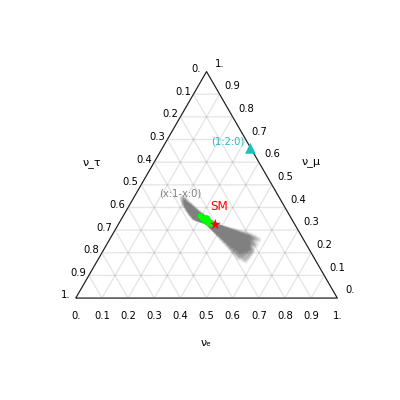

```mathematica
(*Your annotated plot*)Tri1=Show[Tri,Graphics[{Text[Style["SM",Red,FontSize->12],{0.55,0.35}],Text[Style["(x:1-x:0)",Gray,FontSize->10],{0.4,0.4}],Text[Style["(1:2:0)",RGBColor[0.10,0.75,0.75],FontSize->10],{0.58,0.6}]}]]
```

Module to generate various Probability matrix from a given mixing matrices.

```mathematica
getNSIProbMixMatrix[UM_]:=Module[{DNSIPetoe,DNSIPetomu,DNSIPetotau,DNSIPμtoe,DNSIPμtomu,DNSIPμtotau,DNSIPτtoe,DNSIPτtomu,DNSIPτtotau,NSIMixProbmat},
DNSIPetoe =Sum[UM[[1,i]]*Conjugate[UM[[1,i]]]*UM[[1,i]]*Conjugate[UM[[1,i]]],{i,1,3}];
DNSIPetomu =Sum[UM[[2,i]]*Conjugate[UM[[2,i]]]*UM[[1,i]]*Conjugate[UM[[1,i]]],{i,1,3}];
DNSIPetotau =Sum[UM[[3,i]]*Conjugate[UM[[3,i]]]*UM[[1,i]]*Conjugate[UM[[1,i]]],{i,1,3}];
DNSIPμtoe =Sum[UM[[1,i]]*Conjugate[UM[[1,i]]]*UM[[2,i]]*Conjugate[UM[[2,i]]],{i,1,3}];
DNSIPμtomu =Sum[UM[[2,i]]*Conjugate[UM[[2,i]]]*UM[[2,i]]*Conjugate[UM[[2,i]]],{i,1,3}];
DNSIPμtotau =Sum[UM[[3,i]]*Conjugate[UM[[3,i]]]*UM[[2,i]]*Conjugate[UM[[2,i]]],{i,1,3}];
DNSIPτtoe =Sum[UM[[1,i]]*Conjugate[UM[[1,i]]]*UM[[3,i]]*Conjugate[UM[[3,i]]],{i,1,3}];
DNSIPτtomu =Sum[UM[[2,i]]*Conjugate[UM[[2,i]]]*UM[[3,i]]*Conjugate[UM[[3,i]]],{i,1,3}];
DNSIPτtotau =Sum[UM[[3,i]]*Conjugate[UM[[3,i]]]*UM[[3,i]]*Conjugate[UM[[3,i]]],{i,1,3}];
NSIMixProbmat= {{DNSIPetoe,DNSIPetomu,DNSIPetotau},{DNSIPμtoe,DNSIPμtomu,DNSIPμtotau},{DNSIPτtoe,DNSIPτtomu,DNSIPτtotau}};
Return[NSIMixProbmat];];
```

```mathematica
NSIMixProbmat = getNSIProbMixMatrix[UM]
```

(0.800471659646712647398325 | 0.149810037138309227668776 | 0.0497183032149781249328997
0.149810037138309227668776 | 0.434353280151483781150938 | 0.415836682710206991180287
0.0497183032149781249328997 | 0.415836682710206991180287 | 0.534445014074814883886814)

```mathematica
FinRatioNSI=Transpose[NSIMixProbmat].InitRatio;
probNSI = FinRatioNSI/(Sum[FinRatioNSI[[i]],{i,1,3}]);
```

```mathematica
NSIPoints=probNSI[[3]]*vertices[[1]]+probNSI[[1]]*vertices[[2]]+probNSI[[2]]*vertices[[3]];
```

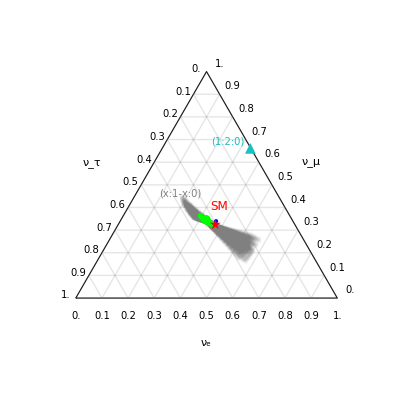

```mathematica
Tri2=Show[Tri1,Graphics[{Blue,Opacity[01],PointSize[Medium],Point[NSIPoints]}]](*Initial Ratio evolved by certain Medium SM mixing angles.*)
```

Module to generate various Mixing Probability matrix in medium due to uncertainty in SM parameters for a given energy and initial ratio.

```mathematica
getNSIRandomPoints[en_,InitRatio_]:=Module[{th12Deg,th13Deg,th23Deg,dCPDeg,PSMMix,UM,DNSIPetoe,DNSIPetomu,DNSIPetotau,DNSIPμtoe,DNSIPμtomu,DNSIPμtotau,DNSIPτtoe,DNSIPτtomu,DNSIPτtotau,NSIMixProbmat,FinRatioNSI,probNSI,NSIPoints,Hf,evc,en1,en2,en3,env,x,y,VPtau,VPmue,VPe,ProbInitRatio,PointInitRatio},th12Deg=RandomReal[{theta12MinDeg,theta12MaxDeg}]*180/π Degree;(*Sample parameters uniformly within its 3-sigma range*)
th13Deg=RandomReal[{theta13MinDeg,theta13MaxDeg}]*180/π Degree;
th23Deg=RandomReal[{theta23MinDeg,theta23MaxDeg}]*180/π Degree;
dCPDeg=RandomReal[{deltaCPMinDeg,deltaCPMaxDeg}]*180/π  Degree;
PSMMix=USMMix/.{ϕ12->th12Deg,ϕ13->th13Deg,ϕ23->th23Deg,δCP->dCPDeg};
PSMMix = Rationalize[PSMMix,10^(-35)](*Rationalizing U to increase Precision.*);
       Kf=PSMMix.Km.ConjugateTranspose[PSMMix](*Kinetic matrix in flavour Basis.*);
       Hf = Kf+Vf(*Total Hamiltonian matrix in flavour Basis.*);
energy = en (*Energy in GeV, L in Km and m in eV.*);
x=5;y=1;
       VPtau =y*Power[10,-10];VPmue =0*y*Power[10,-10];VPe = x*Power[10,-9];(*In eV^2/GeV.*)
       evc=Eigenvectors[N[Hf/.{Vt->VPe,Vu->VPmue,m1->0,Ve->VPe,m2^2->Rationalize[7.59*10^(-5)],m3^2->Rationalize[2.32*10^(-3)],E1->energy},30]];(*Eigenvectors of Hamiltonian matrix in flavour Basis (Not normalized).*)
       en1 = Normalize[evc[[1]]];
en2 = Normalize[evc[[2]]];
en3 = Normalize[evc[[3]]]; (*Normalizing Eigenvectors.*)
       env = {en3,en2,en1} (*Flavour Mixing Matrix.*);UM=ConjugateTranspose[SetPrecision[env,25]] (*Flavour mixing matrix from mass basis to flavour basis.*);DNSIPetoe =Sum[UM[[1,i]]*Conjugate[UM[[1,i]]]*UM[[1,i]]*Conjugate[UM[[1,i]]],{i,1,3}];
DNSIPetomu =Sum[UM[[2,i]]*Conjugate[UM[[2,i]]]*UM[[1,i]]*Conjugate[UM[[1,i]]],{i,1,3}];
DNSIPetotau =Sum[UM[[3,i]]*Conjugate[UM[[3,i]]]*UM[[1,i]]*Conjugate[UM[[1,i]]],{i,1,3}];
DNSIPμtoe =Sum[UM[[1,i]]*Conjugate[UM[[1,i]]]*UM[[2,i]]*Conjugate[UM[[2,i]]],{i,1,3}];
DNSIPμtomu =Sum[UM[[2,i]]*Conjugate[UM[[2,i]]]*UM[[2,i]]*Conjugate[UM[[2,i]]],{i,1,3}];
DNSIPμtotau =Sum[UM[[3,i]]*Conjugate[UM[[3,i]]]*UM[[2,i]]*Conjugate[UM[[2,i]]],{i,1,3}];
DNSIPτtoe =Sum[UM[[1,i]]*Conjugate[UM[[1,i]]]*UM[[3,i]]*Conjugate[UM[[3,i]]],{i,1,3}];
DNSIPτtomu =Sum[UM[[2,i]]*Conjugate[UM[[2,i]]]*UM[[3,i]]*Conjugate[UM[[3,i]]],{i,1,3}];
DNSIPτtotau =Sum[UM[[3,i]]*Conjugate[UM[[3,i]]]*UM[[3,i]]*Conjugate[UM[[3,i]]],{i,1,3}];
NSIMixProbmat= {{DNSIPetoe,DNSIPetomu,DNSIPetotau},{DNSIPμtoe,DNSIPμtomu,DNSIPμtotau},{DNSIPτtoe,DNSIPτtomu,DNSIPτtotau}};
FinRatioNSI=Transpose[NSIMixProbmat].InitRatio;
probNSI = FinRatioNSI/(Sum[FinRatioNSI[[i]],{i,1,3}]);
NSIPoints=probNSI[[3]]*vertices[[1]]+probNSI[[1]]*vertices[[2]]+probNSI[[2]]*vertices[[3]];
ProbInitRatio = InitRatio/(Sum[InitRatio[[i]],{i,1,3}]); (*Initial flavour probability.*)
PointInitRatio=ProbInitRatio[[3]]*vertices[[1]]+ProbInitRatio[[1]]*vertices[[2]]+ProbInitRatio[[2]]*vertices[[3]]; 
Return[{UM,NSIMixProbmat,PointInitRatio,NSIPoints}];];
```

```mathematica
rannum=1000;
NSIRandomPoints=Abs[ParallelTable[getNSIRandomPoints[energy,{1,2,0}],{i,1,rannum}]];
```

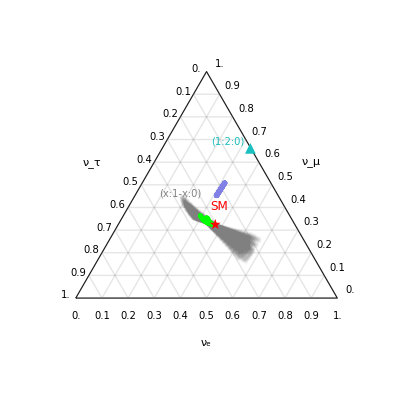

```mathematica
Tri3=Show[Tri1,Graphics[{{RGBColor[0.50,0.50,0.90],Opacity[1],PointSize[Medium],Point[NSIRandomPoints[[1;;-1,-1]]]}}]]
(*Plot for various initial ratio with SM probability evolution.*)
```

```mathematica
(*Custom legend with markers*)
legend=PointLegend[{Red,Gray,RGBColor[0.10,0.75,0.75],Green,RGBColor[0.50,0.50,0.90]},{"SM (1:2:0) Initial Ratio Evolution","Uncertain SM (x:1-x:0) Initial Ratio Evolution","(1:2:0) Initial Ratio","Uncertain SM (1:2:0) Initial Ratio Evolution","v-DM Mixing Evolution (1:2:0) Initial Ratio"},LegendMarkers->{"★","◆","▲","●","●"},(*Circle,diamond,triangle*)LegendLayout->"Column"];

(*Combine the plot and legend side by side*)
Trib=GraphicsRow[{Tri3,legend},Spacings->4]
```

-Graphics-

```mathematica
Tri4=Show[Tri3,Graphics[{{Orange,Opacity[1],PointSize[Large],Point[SMRandomPointsInit[[1;;10,1]]]},{RGBColor[1,0.84,0],Opacity[1],PointSize[Large],Point[listt[[1;;-1,2]]]},{RGBColor[1,0.84,0],Opacity[1],PointSize[Medium],Point[listt[[1;;-1,1]]]},{RGBColor[0.5,0.2,0.7],Opacity[1],PointSize[Large],Point[listm[[1;;-1,2]]]},{RGBColor[0.5,0.2,0.7],Opacity[1],PointSize[Small],Point[listm[[1;;-1,1]]]},{RGBColor[0.3,0.5,0.9],Opacity[1],PointSize[Large],Point[liste[[1;;-1,2]]]},{RGBColor[0.3,0.5,0.9],Opacity[1],PointSize[Medium],Point[liste[[1;;-1,1]]]}}]](*Plot for various initial ratio with SM probability evolution.*)
```

-Graphics-

```mathematica
s1=SMMixProbmat[[3,3]]//ComplexExpand
```

cos^4(δCP) cos^4(ϕ12) sin^4(ϕ13) cos^4(ϕ23)+sin^4(δCP) cos^4(ϕ12) sin^4(ϕ13) cos^4(ϕ23)+cos^4(δCP) sin^4(ϕ12) sin^4(ϕ13) cos^4(ϕ23)+sin^4(δCP) sin^4(ϕ12) sin^4(ϕ13) cos^4(ϕ23)+4 cos^3(δCP) sin^3(ϕ12) cos(ϕ12) sin^3(ϕ13) sin(ϕ23) cos^3(ϕ23)-4 cos^3(δCP) sin(ϕ12) cos^3(ϕ12) sin^3(ϕ13) sin(ϕ23) cos^3(ϕ23)+4 cos(δCP) sin(ϕ12) cos^3(ϕ12) sin(ϕ13) sin^3(ϕ23) cos(ϕ23)+4 sin^2(δCP) cos(δCP) sin^3(ϕ12) cos(ϕ12) sin^3(ϕ13) sin(ϕ23) cos^3(ϕ23)-4 sin^2(δCP) cos(δCP) sin(ϕ12) cos^3(ϕ12) sin^3(ϕ13) sin(ϕ23) cos^3(ϕ23)+12 cos^2(δCP) sin^2(ϕ12) cos^2(ϕ12) sin^2(ϕ13) sin^2(ϕ23) cos^2(ϕ23)+4 sin^2(δCP) sin^2(ϕ12) cos^2(ϕ12) sin^2(ϕ13) sin^2(ϕ23) cos^2(ϕ23)+2 sin^2(δCP) cos^2(δCP) sin^4(ϕ12) sin^4(ϕ13) cos^4(ϕ23)+2 sin^2(δCP) cos^2(δCP) cos^4(ϕ12) sin^4(ϕ13) cos^4(ϕ23)-4 cos(δCP) sin^3(ϕ12) cos(ϕ12) sin(ϕ13) sin^3(ϕ23) cos(ϕ23)+sin^4(ϕ12) sin^4(ϕ23)+cos^4(ϕ12) sin^4(ϕ23)+cos^4(ϕ13) cos^4(ϕ23)

```mathematica
FullSimplify[s1]
```

1/4 (cos^4(δCP) (cos(4 ϕ12)+3) sin^4(ϕ13) cos^4(ϕ23)+4 (sin^4(ϕ12)+cos^4(ϕ12)) (sin^4(δCP) sin^4(ϕ13) cos^4(ϕ23)+sin^4(ϕ23))-4 cos^3(δCP) sin(4 ϕ12) sin^3(ϕ13) sin(ϕ23) cos^3(ϕ23)+4 cos(δCP) sin(4 ϕ12) sin(ϕ13) sin(ϕ23) cos(ϕ23) (sin^2(ϕ23)-sin^2(δCP) sin^2(ϕ13) cos^2(ϕ23))+2 sin^2(δCP) cos^2(δCP) (cos(4 ϕ12)+3) sin^4(ϕ13) cos^4(ϕ23)+(cos(2 δCP)+2) sin^2(2 ϕ12) sin^2(ϕ13) sin^2(2 ϕ23))+cos^4(ϕ13) cos^4(ϕ23)

#### Covariance on Triangle

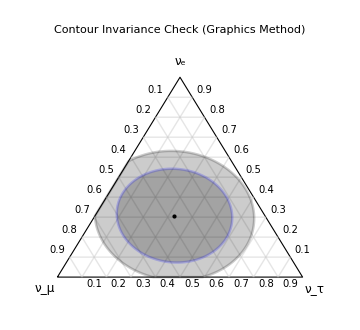

```mathematica
(*---Define Vertices,Labels,Probabilities (Best Fit)---*)vertices={{0,0},{1,0},{0.5,Sqrt[3]/2}};
triangleRegion=Polygon[vertices];
labels={"\!\(\*SubscriptBox[\(ν\), \(μ\)]\)","\!\(\*SubscriptBox[\(ν\), \(τ\)]\)","\!\(\*SubscriptBox[\(ν\), \(e\)]\)"};

(*Best Fit:{fe,fmu,ftau}={0.2,0.39,0.42}*)
(*Map to {fmu,ftau,fe} for vertex mapping*)
bestFitFractions=prob;

(*Convert best fit probabilities to Cartesian coordinates*)
point=bestFitFractions[[1]]*vertices[[1]]+bestFitFractions[[2]]*vertices[[2]]+bestFitFractions[[3]]*vertices[[3]];

(*---Example Covariance Matrices (from previous example)---*)
(*Full 3x3 matrix (conceptual,not directly used) V3x3={{0.010,-0.004,-0.006},(*fe row*){-0.004,0.015,-0.011},(*fmu row*){-0.006,-0.011,0.017}}  (*ftau row*)*)

(*2x2 Submatrices for different bases*)
covFeFmu=0.1{{0.010,-0.004},{-0.004,0.015}}; (*Basis {fe,fmu}*)
covFeFtau=0.1{{0.010,-0.006},{-0.006,0.017}}; (*Basis {fe,ftau}*)
covFmuFtau=0.1{{0.015,-0.011},{-0.011,0.017}}; (*Basis {fmu,ftau}*)

confidenceLevel=0.68; (*1-sigma*)

(*---Define Transformation Matrices (Jacobians)---*)

(*From {fmu,ftau} to {x,y}*)
(*Pxy=V3+fmu*(V1-V3)+ftau*(V2-V3)*)
TmuTau=Transpose[{vertices[[1]]-vertices[[3]],vertices[[2]]-vertices[[3]]}];

(*From {fe,fmu} to {x,y}*)
(*fe=1-fmu-ftau=>ftau=1-fe-fmu*)
(*Pxy=fmu*V1+(1-fe-fmu)*V2+fe*V3*)
(*Pxy=V2+fe*(V3-V2)+fmu*(V1-V2)*)
TfeFmu=Transpose[{vertices[[3]]-vertices[[2]],vertices[[1]]-vertices[[2]]}];

(*From {fe,ftau} to {x,y}*)
(*fmu=1-fe-ftau*)
(*Pxy=(1-fe-ftau)*V1+ftau*V2+fe*V3*)
(*Pxy=V1+fe*(V3-V1)+ftau*(V2-V1)*)
TfeFtau=Transpose[{vertices[[3]]-vertices[[1]],vertices[[2]]-vertices[[1]]}];

(*---Transform Covariance Matrices to Cartesian {x,y}---*)
covXYfromMuTau=TmuTau.covFmuFtau.Transpose[TmuTau];
covXYfromFeMu=TfeFmu.covFeFmu.Transpose[TfeFmu];
covXYfromFeTau=TfeFtau.covFeFtau.Transpose[TfeFtau];


(*---Keep Your Helper Functions (drawGridLines,ConfidenceEllipse)---*)
drawGridLines[n_]:=(*... your code...*)Module[{lines={},numbers={},edge1,edge2,edge3},edge1={vertices[[1]],vertices[[2]]};edge2={vertices[[2]],vertices[[3]]};edge3={vertices[[3]],vertices[[1]]};Do[AppendTo[lines,Line[{vertices[[1]]+i/n (vertices[[2]]-vertices[[1]]),vertices[[1]]+i/n (vertices[[3]]-vertices[[1]])}]];AppendTo[lines,Line[{vertices[[2]]+i/n (vertices[[1]]-vertices[[2]]),vertices[[2]]+i/n (vertices[[3]]-vertices[[2]])}]];AppendTo[lines,Line[{vertices[[3]]+i/n (vertices[[1]]-vertices[[3]]),vertices[[3]]+i/n (vertices[[2]]-vertices[[3]])}]];AppendTo[numbers,Text[Style[N[i/n],10],vertices[[1]]+i/n (edge1[[2]]-edge1[[1]])+{0.05,-0.03}]];(*Adjusted offset*)AppendTo[numbers,Text[Style[N[i/n],10],vertices[[2]]+i/n (edge2[[2]]-edge2[[1]])+{0.05,0.03}]];AppendTo[numbers,Text[Style[N[i/n],10],vertices[[3]]+i/n (edge3[[2]]-edge3[[1]])+{-0.05,0.03}]];(*Adjusted offset*),{i,1,n-1}];{lines,numbers}];
ConfidenceEllipse[pointXY_,covXY_,level_]:=Module[{chi2,sqrtCov,ellipse,clippedRegion,areaCheck},(*Check if the covariance matrix is numeric and 2x2*)If[!MatrixQ[covXY,NumericQ]||Dimensions[covXY]!={2,2},Return[Nothing,Module]];
chi2=InverseCDF[ChiSquareDistribution[2],level];
(*Use Check to gracefully handle potential errors in MatrixPower*)sqrtCov=Check[MatrixPower[covXY,1/2],$Failed];
If[sqrtCov===$Failed,Print["Warning: Could not compute matrix square root for covariance: ",MatrixForm[covXY]];
Return[Nothing,Module]];
ellipse=Ellipsoid[pointXY,Sqrt[chi2]*sqrtCov];
(*Use Check for RegionIntersection as well*)clippedRegion=Check[RegionIntersection[ellipse,triangleRegion],$Failed];
If[clippedRegion===$Failed,Print["Warning: RegionIntersection failed."];
Return[Nothing,Module]];
(*Check if the resulting region is valid and has non-negligible area*)areaCheck=Check[Area[clippedRegion],0];
If[!RegionQ[clippedRegion]||!NumericQ[areaCheck]||areaCheck<=1*^-9,Return[Nothing,Module]];
(*If all checks pass,return the graphics directives*){Opacity[0.2],EdgeForm[{Which[level==0.68,Directive[Blue,Thick],level==0.95,Directive[Red,Dashed,Thick],True,Black],Thickness[0.005]}],BoundaryDiscretizeRegion[clippedRegion,MaxCellMeasure->0.001]}]

(*---Plot the triangle with transformed ellipses---*)
Graphics[{(*Base Triangle and Grid*){EdgeForm[Black],FaceForm[None],Polygon[vertices]},{GrayLevel[0.8],Opacity[0.5],drawGridLines[10][[1]]},{Black,drawGridLines[10][[2]]},(*Labels*){Text[Style[labels[[1]],12],vertices[[1]]+{-0.05,-0.05}]},(*Fmu bottom-left*){Text[Style[labels[[2]],12],vertices[[2]]+{0.05,-0.05}]},(*Ftau bottom-right*){Text[Style[labels[[3]],12],vertices[[3]]+{0,0.07}]},(*Fe top*)(*Ellipses-using TRANSFORMED covariance matrices*)ConfidenceEllipse[point,3covXYfromMuTau,1.1confidenceLevel],ConfidenceEllipse[point,covXYfromFeMu,confidenceLevel],(*Best Fit Point*){Black,PointSize[Large],Point[point]}},Axes->False,PlotRange->{{-0.1,1.1},{-0.1,1.0}},(*Adjusted range slightly*)AspectRatio->Automatic,PlotLabel->Style["Contour Invariance Check (Graphics Method)",14,Bold],ImageSize->Medium]
```

#### CSV Data on Flavour triangle

```mathematica
(*Define the vertices of the flavor triangle*)vertices={{0,0},{1,0},{0.5,Sqrt[3]/2}};

(*Define the triangle region for clipping*)
triangleRegion=Polygon[vertices];

(*Define the labels for the vertices*)
labels={"\!\(\*SubscriptBox[\(ν\), \(μ\)]\)","\!\(\*SubscriptBox[\(ν\), \(τ\)]\)","\!\(\*SubscriptBox[\(ν\), \(e\)]\)"};

(*Define the probabilities for each flavor*)
probabilities={0.5,0.3,0.2};
probabilities2={0.3,0.2,0.5};

(*Convert probabilities to Cartesian coordinates*)
point=probabilities[[1]]*vertices[[1]]+probabilities[[2]]*vertices[[2]]+probabilities[[3]]*vertices[[3]];
point2=probabilities2[[1]]*vertices[[1]]+probabilities2[[2]]*vertices[[2]]+probabilities2[[3]]*vertices[[3]];

(*Function to draw grid lines and numbers*)
drawGridLines[n_]:=Module[{lines={},numbers={},edge1,edge2,edge3},edge1={vertices[[1]],vertices[[2]]};
edge2={vertices[[2]],vertices[[3]]};
edge3={vertices[[3]],vertices[[1]]};
Do[AppendTo[lines,Line[{vertices[[1]]+i/n (vertices[[2]]-vertices[[1]]),vertices[[1]]+i/n (vertices[[3]]-vertices[[1]])}]];
AppendTo[lines,Line[{vertices[[2]]+i/n (vertices[[1]]-vertices[[2]]),vertices[[2]]+i/n (vertices[[3]]-vertices[[2]])}]];
AppendTo[lines,Line[{vertices[[3]]+i/n (vertices[[1]]-vertices[[3]]),vertices[[3]]+i/n (vertices[[2]]-vertices[[3]])}]];
AppendTo[numbers,Text[Style[N[i/n],10],vertices[[1]]+i/n (edge1[[2]]-edge1[[1]])+{0,-0.07}]];
AppendTo[numbers,Text[Style[N[i/n],10],vertices[[2]]+i/n (edge2[[2]]-edge2[[1]])+{0.05,0.03}]];
AppendTo[numbers,Text[Style[N[i/n],10],vertices[[3]]+i/n (edge3[[2]]-edge3[[1]])+{-0.04,0.01}]];,{i,0,n}];
{lines,numbers}];

(*Function to create clipped confidence ellipses*)
ConfidenceEllipse[point_,cov_,level_]:=Module[{chi2=InverseCDF[ChiSquareDistribution[2],level],ellipse,clippedRegion},ellipse=Ellipsoid[point,Sqrt[chi2]*cov];
clippedRegion=RegionIntersection[ellipse,triangleRegion];
If[RegionMeasure[clippedRegion]>0,{Opacity[0.1],EdgeForm[{If[level==0.95,Dotted,Thick],Black}],BoundaryDiscretizeRegion[clippedRegion]},Nothing]];

(*Plot the triangle with clipped ellipses*)
Graphics[{{EdgeForm[Black],FaceForm[None],Polygon[vertices]},{Gray,Opacity[0.2],drawGridLines[10][[1]]},{Black,drawGridLines[10][[2]]},{Text[labels[[1]],vertices[[1]]+{0.5,-0.17}]},{Text[labels[[2]],vertices[[2]]+{-0.1,0.52}]},{Text[labels[[3]],vertices[[3]]+{-0.44,-0.35}]},{Blue,ConfidenceEllipse[point,{{0.01,-0.004},{-0.004,0.015}},0.68]},{Blue,ConfidenceEllipse[point,{{0.01,-0.006},{-0.006,0.017}},0.68]},{Blue,ConfidenceEllipse[point,{{0.015,-0.011},{-0.011,0.017}},0.68]},{Green,ConfidenceEllipse[point2,{{0.02,-0.01},{-0.01,0.015}},0.68]},{Green,ConfidenceEllipse[point2,{{0.02,-0.01},{-0.01,0.015}},0.95]},{Red,PointSize[Large],Point[point]},{Green,PointSize[Large],Point[point2]},{Black,PointSize[Small],Point[dataPoints]}},Axes->False,PlotRange->{{-0.15,1.1},{-0.25,1.0}},AspectRatio->Automatic]
```

-Graphics-

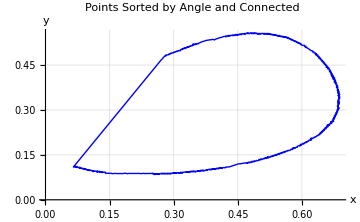

```mathematica
(*filePath="C:\\Users\\YourName\\Documents\\Mathematica\\contour_points.csv";*)(*Option B:Relative Path (if the CSV is in Mathematica's current directory)*)(*filePath="contour_points.csv";*)(*Option C:Use the Menu (Insert->File Path...) and paste the result here*)filePath="/home/as/Default Dataset.csv";


(*---Step 2:Import the Data---*)

(*Use Import with {"CSV","Data"}-this is usually robust and handles headers*)
(*It attempts to interpret columns as numeric data*)
dataPoints=Import[filePath,{"CSV","Data"}];

(*Calculate the centroid (average point)*)centroid=Mean[dataPoints];

(*Define a function to get the angle relative to the centroid*)
(*ArcTan[x,y] gives angle in (-Pi,Pi]*)
angle[{x_,y_}]:=ArcTan[x-centroid[[1]],y-centroid[[2]]];

(*Sort the data points by angle*)
sortedPoints=SortBy[dataPoints,angle];

(*Close the loop*)
closedSortedPoints=Append[sortedPoints,First[sortedPoints]];

(*Plot the sorted points connected by lines*)
ListPlot[closedSortedPoints,Joined->True,PlotStyle->{Thick,Blue},AxesLabel->{"x","y"},PlotLabel->"Points Sorted by Angle and Connected",GridLines->Automatic,BaseStyle->FontSize->12,ImageSize->Medium(*Show original points*)]
```

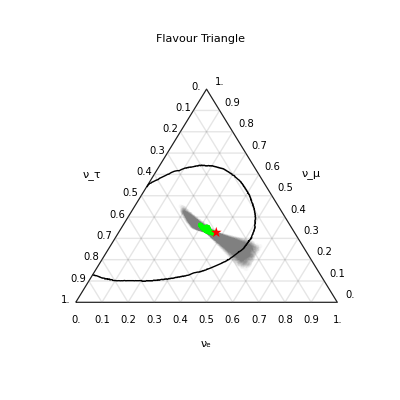

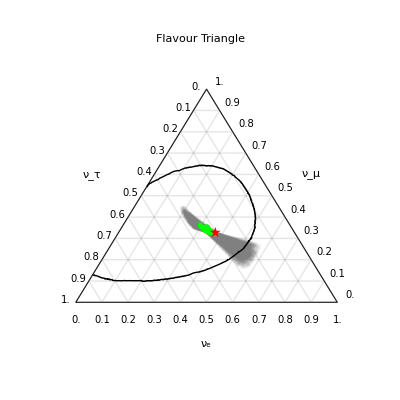

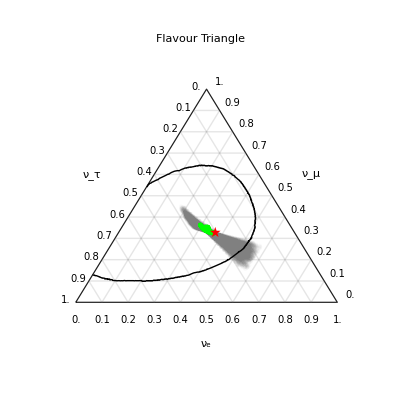

```mathematica
(*---Step 1:Order the Points (Heuristic:Sort by Angle)---*)centroid=Mean[dataPoints];
angle[{x_,y_}]:=ArcTan[x-centroid[[1]],y-centroid[[2]]];
sortedPoints=SortBy[dataPoints,angle];

(*---Step 2:Create an OPEN B-Spline Function---*)
(*Do NOT append the first point*)
(*SplineClosed->False (or omit,as False is default)*)
splineFuncOpen=BSplineFunction[sortedPoints,SplineDegree->3,SplineClosed->False];

(*---Step 3:Plot the OPEN Spline using ParametricPlot---*)
(*Determine the parameter range for the open spline*)
(*It's often related to the number of points,check splineFuncOpen[[2]] if needed,but {0,1} often works*)
{tmin,tmax}={0,1}; (*Default parameter range for BSplineFunction*)
(*Check if the function provides its own range:*)
(*If[Head[splineFuncOpen[[2]]]===List&&Length[splineFuncOpen[[2]]]==1&&Head[splineFuncOpen[[2,1]]]===List&&Length[splineFuncOpen[[2,1]]]==2,{tmin,tmax}=splineFuncOpen[[2,1]]]*)


plotSplineOpen=ParametricPlot[splineFuncOpen[t],{t,tmin,tmax},(*Parameter t goes over the spline's range*)PlotStyle->{Black,Thick},Axes->True,AxesLabel->{"x","y"},PlotLabel->"Smoothed Open Curve from Digitized Points",GridLines->Automatic,BaseStyle->FontSize->12,ImageSize->Medium,PlotRange->All];

(*---Optional:Show Original Points---*)
plotOriginalPoints=ListPlot[dataPoints,PlotStyle->{Red,PointSize[Medium]}];


(*---Combine---*)
Show[Tri,plotSplineOpen,PlotLabel->"Flavour Triangle"]
```

## COM Energy

```mathematica
mv = 0.1; (*eV*)
En1 = 10^(16) (*10 PeV in eV*)
```

10000000000000000

```mathematica
COM[y_,x_]:=Sqrt[mv^2+y^2+2*x*y](*eV*)
```

```mathematica
COM[10^(-22),10^(15)]
```

0.100001

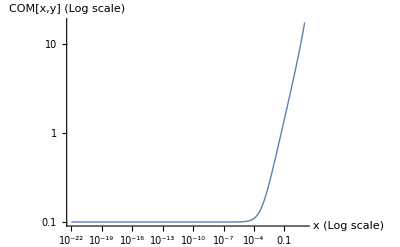

```mathematica
LogLogPlot[COM[x,10^1],{x,10^(-22),10},PlotRange->All,AxesLabel->{"x (Log scale)","COM[x,y] (Log scale)"},PlotStyle->Thick]
```

```mathematica
Manipulate[LogLogPlot[COM[x,10^y],{x,10^(-22),10},PlotRange->All,AxesLabel->{"mχ (eV)","√_s (eV)"},PlotStyle->Thick,GridLines->Automatic,PlotLabel->StringForm["COM[mχ,En] for ν Energy (GeV) = ``",NumberForm[10^(y-9),{3,2}]]],{{y,9,"log10(y)"},9,17,1,Appearance->"Labeled"}]
```

```mathematica
coupling2[x_,y_]:=1/3 * 10^(6) *x^2*y//N
```

```mathematica
V = 10^(-18);
```

```mathematica
Manipulate[LogLogPlot[V*coupling2[10^y,x],{x,10^(-22),10},PlotRange->All,AxesLabel->{"mχ (eV)","g*f"},PlotStyle->Thick,GridLines->Automatic,PlotLabel->StringForm["mZ' (eV) = ``",NumberForm[10^(y),{3,2}]]],{{y,0,"log10(y)"},0,6,1,Appearance->"Labeled"}]
```